```mathematica
Clear["`*"]
```

```mathematica
timeList=Import["/home/bczhc/t/ncm data dump/playlist/2666362456/at","Text"];
```

```mathematica
timeList=StringSplit[timeList,"\n"];
```

```mathematica
intItpr=Interpreter["Integer"];
```

```mathematica
timestamps=((intItpr@#)/1000&)/@timeList;
```

```mathematica
timeList=(FromUnixTime[#,TimeZone->+8]&)/@timestamps;
```

```mathematica
hours=DateValue[#,"HourExact"]&/@timeList;
```

```mathematica
data=MapThread[{#1,#2}&,{timeList,hours}];
```

```mathematica
ts=TimeSeries[data];
```

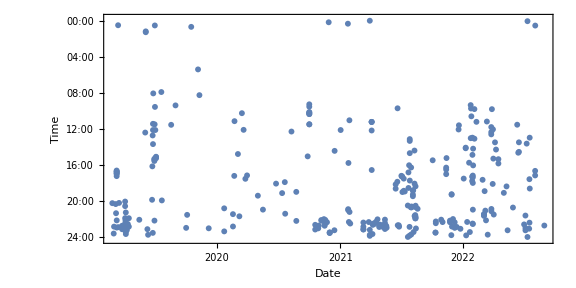

```mathematica
DateListPlot[
ts,
Joined->False,
ScalingFunctions->"Reverse",
AspectRatio->1/2,
FrameLabel->{"Date","Time"},
ImageSize->Large,
FrameTicks->{
{Table[{x,StringRepeat["0",2-StringLength[ToString@x]]<>ToString@x<>":00"},{x,0,24,2}],None},{Automatic,None}
},
PlotRange->{Automatic,{-0.2,24.2}}
]
```

```mathematica
groups=GroupBy[DateObject@DateValue[#,{"Year","Month","Day"}]&/@timeList,#&];
```

```mathematica
data=KeyValueMap[{#1,#2}&,Length/@groups];
```

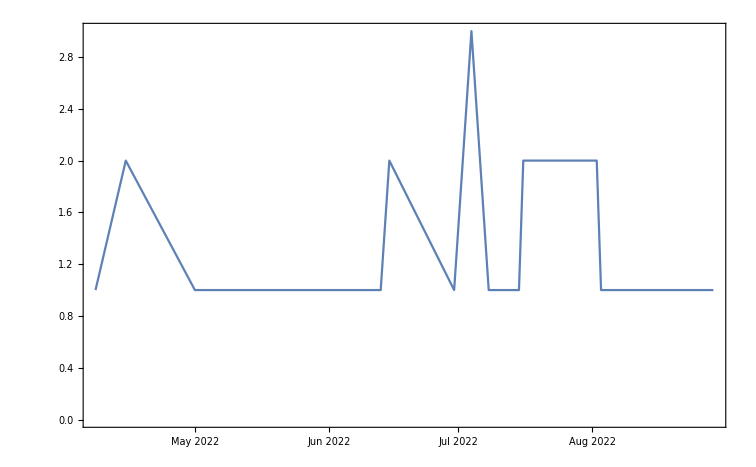

```mathematica
DateListPlot[data[[1;;20]]]
```

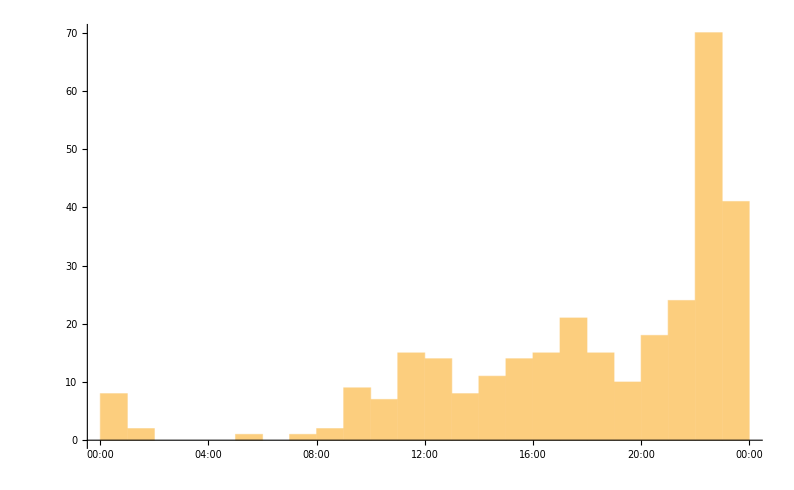

```mathematica
DateHistogram[timeList,"Hour",DateReduction->"Day"]
```